### Start choosing the example:

```mathematica
t=25;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

EliminatorX: Good job!

DataToEquations: Done.

{0.026026,Null}

```mathematica
v0=MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1606→0,j1607→2-1,j1608→1,j1609→1,j1610→2,j1611→2-1,j1612→0,j1613→0,j1614→0,j1615→0,jt1616→2-1,jt1617→0,jt1618→0,jt1619→0,jt1620→0,jt1621→0,jt1622→2-1,jt1623→1,jt1624→1,jt1625→0,u1626→5,u1627→5,u1628→6,u1629→5,u1630→6,u1631→2-1+5,u1632→5,u1633→-1+6,u1634→5,u1635→6|>

#### Non-linear case

```mathematica
alpha = 2;
beta = 0;
A = 0.2;
Parameters["alpha"] = alpha;
Parameters
```

<|alpha→2,beta→0,g[m]→Log,W[x,A]→Function[{x,a},a Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$177811[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$177811[x$]-g$177811[m$]]|>

```mathematica
MFGEquations["Nrhs"]
```

{j1606-j1611+Intg[j1606-j1611],j1608-j1613+Intg[j1608-j1613]}

```mathematica
FixedSolverStepX1[MFGEquations]@ MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1610→2,u1632→5,u1634→5,j1606→0,j1607→2-1,j1609→1,j1611→2-1,j1612→0,j1613→0,j1614→0,j1615→0,jt1616→2-1,jt1617→0,jt1618→0,jt1619→0,jt1620→0,jt1621→0,jt1622→2-1,jt1623→1,jt1624→1,jt1625→0,u1627→5,u1629→5,u1631→2-1+5,u1633→-1+6,u1635→6,j1608→1,u1626→5,u1628→6,u1630→6|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1606→0,j1607→2-1,j1608→1.,j1609→1,j1610→2,j1611→2-1,j1612→0,j1613→0,j1614→0,j1615→0,jt1616→2-1,jt1617→0,jt1618→0,jt1619→0,jt1620→0,jt1621→0,jt1622→2-1,jt1623→1,jt1624→1,jt1625→0,u1626→5.,u1627→5,u1628→6.82668,u1629→5,u1630→6.82668,u1631→2-1+5,u1632→5,u1633→-1+6,u1634→5,u1635→6|>

```mathematica
FixedSolverStepX1[MFGEquations]@%//KeySort
```

<|j1606→0,j1607→2-1,j1608→1.,j1609→1,j1610→2,j1611→2-1,j1612→0,j1613→0,j1614→0,j1615→0,jt1616→2-1,jt1617→0,jt1618→0,jt1619→0,jt1620→0,jt1621→0,jt1622→2-1,jt1623→1,jt1624→1,jt1625→0,u1626→5.,u1627→5,u1628→6.82668,u1629→5,u1630→6.82668,u1631→2-1+5,u1632→5,u1633→-1+6,u1634→5,u1635→6|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1606→0,j1607→2-1,j1608→1.,j1609→1,j1610→2,j1611→2-1,j1612→0,j1613→0,j1614→0,j1615→0,jt1616→2-1,jt1617→0,jt1618→0,jt1619→0,jt1620→0,jt1621→0,jt1622→2-1,jt1623→1,jt1624→1,jt1625→0,u1626→5.,u1627→5,u1628→6.82668,u1629→5,u1630→6.82668,u1631→2-1+5,u1632→5,u1633→-1+6,u1634→5,u1635→6|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]]//N,11, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.,u1630→6.|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1610→2.,u1632→5.,u1634→5.,j1606→0.,j1607→1.,j1609→1.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1627→5.,u1629→5.,u1631→6.,u1633→5.,u1635→6.,j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668|>

{j1608→1.,u1626→5.,u1628→6.82668,u1630→6.82668}

<|j1606→0.,j1607→1.,j1608→1.,j1609→1.,j1610→2.,j1611→1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→1.,jt1623→1.,jt1624→1.,jt1625→0.,u1626→5.,u1627→5.,u1628→6.82668,u1629→5.,u1630→6.82668,u1631→6.,u1632→5.,u1633→5.,u1634→5.,u1635→6.|>

```mathematica
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol1
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol2
(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]])/.nsol3n
```

0.826677

3.14018×10^-16

1.58522

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j1606-j1611-u1626+u1631==0.826677&&j1608-j1613-u1628+u1633==-0.826677

<|j1606→0.,j1607→2.-1. 1.,j1608→1.,j1609→0.+1. 1.,j1610→2.,j1611→2.-1. 1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→2.-1. 1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→2.-1. 1.,jt1623→0.+1. 1.,jt1624→0.+1. 1.,jt1625→0.,u1626→5.,u1627→5,u1628→6.82668,u1629→5,u1630→6.82668,u1631→2.82668-1. 1.+1. 5.,u1632→5,u1633→-0.826677-1. 1.+1. 6.82668,u1634→5,u1635→6.82668|>

```mathematica
nsol3n=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced1"][[2]],10, SameTest->(Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<10^(-17)&)]//KeySort
```

FixedX3: next step: j1606-j1611-u1626+u1631==-0.294244&&j1608-j1613-u1628+u1633==0.294244

FixedX3: next step: j1606-j1611-u1626+u1631==-0.294244&&j1608-j1613-u1628+u1633==0.294244

<|j1606→0.,j1607→2.-1. 1.,j1608→1.,j1609→0.+1. 1.,j1610→2.,j1611→2.-1. 1.,j1612→0.,j1613→0.,j1614→0.,j1615→0.,jt1616→2.-1. 1.,jt1617→0.,jt1618→0.,jt1619→0.,jt1620→0.,jt1621→0.,jt1622→2.-1. 1.,jt1623→0.+1. 1.,jt1624→0.+1. 1.,jt1625→0.,u1626→5.,u1627→5,u1628→5.70576,u1629→5,u1630→5.70576,u1631→1.70576-1. 1.+1. 5.,u1632→5,u1633→0.294244-1. 1.+1. 5.70576,u1634→5,u1635→5.70576|>

### What is this plot for?

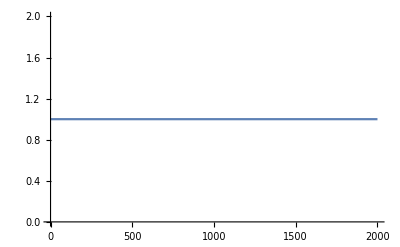
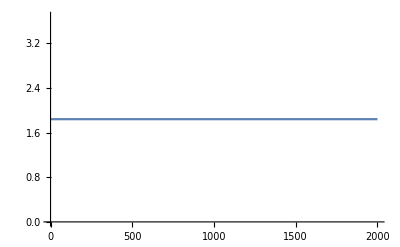
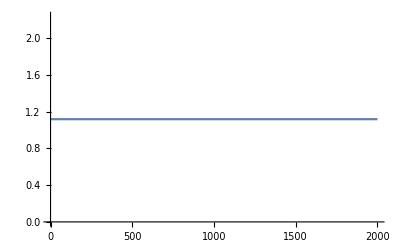
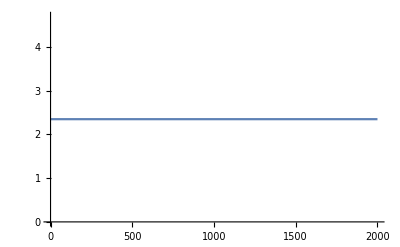
<|{2,1->2}→-Graphics-,{ex746,1->ex746}→-Graphics-,{3,2->3}→-Graphics-,{ex747,3->ex747}→-Graphics-,{2,en745->2}→-Graphics-,{1,1->2}→-Graphics-,{1,1->ex746}→-Graphics-,{2,2->3}→-Graphics-,{3,3->ex747}→-Graphics-,{en745,en745->2}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.

```mathematica
f=<|c->b|>
```

<|c→b|>

```mathematica
AssociateTo[f,v->m]
```

<|c→b,v→m|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
Append[f,m->b]
```

<|c→b,v→m,m→b|>

```mathematica
f
```

<|c→b,v→m|>

```mathematica
AssociateTo[f,m->b]
```

<|c→b,v→m,m→b|>

```mathematica
f
```

<|c→b,v→m,m→b|>

```mathematica
f=Append[f,g->k]
```

<|c→b,v→m,m→b,g→k|>

```mathematica
f
```

<|c→b,v→m,m→b,g→k|>

```mathematica
Reduce[j589==0.+1. j589&&j589==0.+1. j589]
```

True

```mathematica
Solve[x^3 ==1, Reals]
```

{{x→1}}

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

EqEliminartorX2: Count!

EqEliminatorX2: Number of solutions: 2
The system is: Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[Reduce[NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[j592]&&NonNegative[2-j592]&&NonNegative[2-j592]&&NonNegative[5-u607]&&NonNegative[-u609+u612]&&NonNegative[-u611+u612]&&NonNegative[u609-u612]&&NonNegative[u609-u611]&&NonNegative[5-u614]&&(j592==0||-5+u607==0)&&(j592==0||u611-u612==0)&&(2-j592==0||-u609+u611==0)&&(2-j592==0||-5+u614==0)&&(#1==#2&)&&{{-j592-u607+u612,2-j592-u609+u614},{-j592+Intg[-j592],2-j592+Intg[2-j592]}/.MFGraphs`Private`criticalreduced2$31761⟦2⟧},ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ],ℝ]

$Aborted